# Create Data

## Program

### load

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

### R <-> MMA

```mathematica
makeClusterFromRdata[rdata_]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,Drop[rdata,1]],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"Nohead"]:=Map[Drop[#,-1]&,Gather[Map[Drop[#,1]&,rdata],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,"NoID"]:=Map[Drop[#,-1]&,Gather[Drop[rdata,1],#1[[-1]]==#2[[-1]]&],{2}]
```

```mathematica
makeClusterFromRdata[rdata_,op__]:=If[
Length[Flatten[Union[{{op},{"NoID","Nohead"}}]]]==2,
Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]
]
```

```mathematica
(*makeClusterFromRdata[rdata_,"NoID","Nohead"]:=Map[Drop[#,-1]&,Gather[rdata,#1[[-1]]==#2[[-1]]&],{2}]*)
```

```mathematica
makeRClusterFromMMAClData[cl_List]:=Module[
{len,dim,ClIDs},
len=Length[cl];
dim=Length[cl[[1,1]]];
ClIDs=Table[i,{i,len}];
Flatten[Table[Map[Append[#,i]&,cl[[i]]],{i,len}],1]
]
```

```mathematica
createClusterdFileR[li_]:=Flatten[Table[Map[Append[#,n]&,li[[n]]],{n,Length[li]}],1]
```

## Prepare

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation/data"]
```

/Users/amanokou/gitsrc/ClusteringAdequation/data

## 100D, single length, @10

```mathematica
(slenCl[100][10]=Map[Table[#,{10}]&,IdentityMatrix[100]])//Dimensions
```

{100,10,100}

```mathematica
Export["singleLen_100D_10x.tsv",makeRClusterFromMMAClData[slenCl[100][10]]]
```

singleLen_100D_10x.tsv

## 500D, single length, @10

```mathematica
(slenCl[500][10]=Map[Table[#,{10}]&,IdentityMatrix[500]])//Dimensions
```

{500,10,500}

```mathematica
Export["singleLen_500D_10x.tsv",makeRClusterFromMMAClData[slenCl[500][10]]]
```

singleLen_500D_10x.tsv

```mathematica
(slenClR[500][10]=makeRClusterFromMMAClData[slenCl[500][10]])//Dimensions
```

{5000,501}

inncorrect data

```mathematica
slenClRI[500][10][1]=ReplacePart[slenClR[500][10],{{1,501}->501,{2,501}->501,{3,501}->501,{4,501}->501,{5,501}->501}];
```

```mathematica
Export["singleLen_i1_500D_10x.tsv",slenClRI[500][10][1]]
```

singleLen_i1_500D_10x.tsv

## 10D, single length, @1

```mathematica
slen[10][1]=IdentityMatrix[10];
```

```mathematica
slenCl[10][1]=Map[{#}&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_1x.tsv",makeRClusterFromMMAClData[slenCl[10][1]]]*)
```

singleLen_10D_1x.tsv

## 10D, single length, @2

```mathematica
slenCl[10][2]=Map[Table[#,{2}]&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_2x.tsv",makeRClusterFromMMAClData[slenCl[10][2]]]*)
```

singleLen_10D_2x.tsv

## 10D, single length, @4

```mathematica
slenCl[10][4]=Map[Table[#,{4}]&,slen[10][1]]
```

{{{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0}},{{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0}},{{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0}},{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0}},{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1}}}

```mathematica
(*Export["singleLen_10D_4x.tsv",makeRClusterFromMMAClData[slenCl[10][4]]]*)
```

singleLen_10D_4x.tsv

## 10D, single length, @8

```mathematica
slenCl[10][8]=Map[Table[#,{8}]&,slen[10][1]];
```

```mathematica
(*Export["singleLen_10D_8x.tsv",makeRClusterFromMMAClData[slenCl[10][8]]]*)
```

singleLen_10D_8x.tsv

## 4D, single length, @1

```mathematica
slen[4][1]=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
slenCl[4][1]=Map[{#}&,slen[4][1]]
```

{{{1,0,0,0}},{{0,1,0,0}},{{0,0,1,0}},{{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_1x.tsv",makeRClusterFromMMAClData[slenCl[4][1]]]*)
```

singleLen_4D_1x.tsv

## 4D, single length, @2

```mathematica
slenCl[4][2]=Map[Table[#,{2}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_2x.tsv",makeRClusterFromMMAClData[slenCl[4][2]]]*)
```

singleLen_4D_2x.tsv

## 4D, single length, @4

```mathematica
slenCl[4][4]=Map[Table[#,{4}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_4x.tsv",makeRClusterFromMMAClData[slenCl[4][4]]]*)
```

singleLen_4D_4x.tsv

## 4D, single length, @8

```mathematica
slenCl[4][8]=Map[Table[#,{8}]&,slen[4][1]]
```

{{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0},{0,0,1,0}},{{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1},{0,0,0,1}}}

```mathematica
(*Export["singleLen_4D_8x.tsv",makeRClusterFromMMAClData[slenCl[4][8]]]*)
```

singleLen_4D_8x.tsv

## 3D, single length, @1

```mathematica
slen[3][1]=IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
slenCl[3][1]=Map[{#}&,slen[3][1]]
```

{{{1,0,0}},{{0,1,0}},{{0,0,1}}}

```mathematica
(*Export["singleLen_3D_1x.tsv",makeRClusterFromMMAClData[slenCl[3][1]]]*)
```

singleLen_3D_1x.tsv

## 3D, single length, @2

```mathematica
slenCl[3][2]=Map[Table[#,{2}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0}},{{0,1,0},{0,1,0}},{{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_2x.tsv",makeRClusterFromMMAClData[slenCl[3][2]]]*)
```

singleLen_3D_2x.tsv

## 3D, single length, @4

```mathematica
slenCl[3][4]=Map[Table[#,{4}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0},{1,0,0},{1,0,0}},{{0,1,0},{0,1,0},{0,1,0},{0,1,0}},{{0,0,1},{0,0,1},{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_4x.tsv",makeRClusterFromMMAClData[slenCl[3][4]]]*)
```

singleLen_3D_4x.tsv

## 3D, single length, @8

```mathematica
slenCl[3][8]=Map[Table[#,{8}]&,slen[3][1]]
```

{{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0}},{{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0}},{{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}}

```mathematica
(*Export["singleLen_3D_8x.tsv",makeRClusterFromMMAClData[slenCl[3][8]]]*)
```

singleLen_3D_8x.tsv

## 2D, background, 200 - 1000; 200

```mathematica
bg[2][200]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{200}];
```

```mathematica
bg[2][400]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{400}];
```

```mathematica
bg[2][600]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{600}];
```

```mathematica
bg[2][800]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{800}];
```

```mathematica
bg[2][1000]=Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{1000}];
```

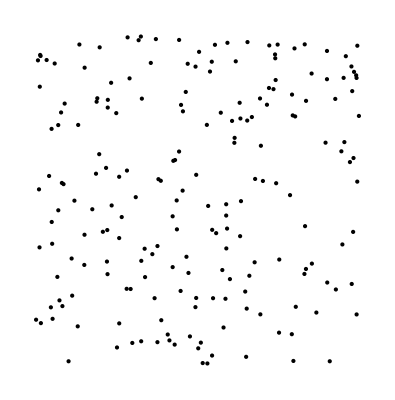

```mathematica
Graphics[Map[Point[#]&,bg[2][200]]]
```

```mathematica
(*Export["bg-2-200.tsv",bg[2][200]]*)
```

```mathematica
(*Export["bg-2-400.tsv",bg[2][400]]*)
```

```mathematica
(*Export["bg-2-600.tsv",bg[2][600]]*)
```

```mathematica
(*Export["bg-2-800.tsv",bg[2][800]]*)
```

```mathematica
(*Export["bg-2-1000.tsv",bg[2][1000]]*)
```

## 2D, normaldist;single, 2 - 20; 2

```mathematica
nd[2][2]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{2}];
```

```mathematica
For[i=2,i≤20,i+=2,Print[i];
nd[2][i]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{i}];
]
```

2

4

6

8

10

12

14

16

18

20

## 2D, normaldist;single, 200 - 1600; 200

```mathematica
nd[2][200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{200}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{400}];
```

```mathematica
nd[2][600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{600}];
```

```mathematica
nd[2][800]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{800}];
```

```mathematica
nd[2][1000]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1000}];
```

```mathematica
nd[2][1200]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1200}];
```

```mathematica
nd[2][1400]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1400}];
```

```mathematica
nd[2][1600]=Table[{RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{1600}];
```

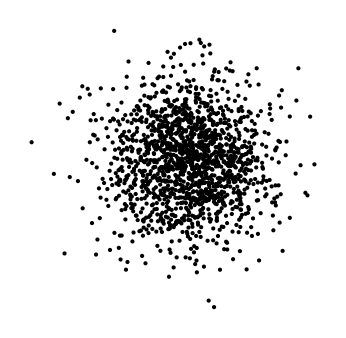

```mathematica
Graphics[Map[Point[#]&,nd[2][1600]]]
```

## 2D, 3Cls

```mathematica
correctdata[2][2][3]={Map[#+{0,0}&,nd[2][2]],Map[#+{5,0}&,nd[2][2]],Map[#+{2.5,3.5}&,nd[2][2]]}
```

{{{1.03626,0.979027},{0.231624,0.00717042}},{{6.03626,0.979027},{5.23162,0.00717042}},{{3.53626,4.47903},{2.73162,3.50717}}}

```mathematica
makeRClusterFromMMAClData[correctdata[2][2][3]]
```

{{1.03626,0.979027,1},{0.231624,0.00717042,1},{6.03626,0.979027,2},{5.23162,0.00717042,2},{3.53626,4.47903,3},{2.73162,3.50717,3}}

```mathematica
Directory[]
```

/Users/amanokou

```mathematica
(*Export["correctdata_2_2_3.tsv",correctdata[2][2][3]//makeRClusterFromMMAClData]*)
```

```mathematica
correctdata[2][4][3]={Map[#+{0,0}&,nd[2][4]],Map[#+{5,0}&,nd[2][4]],Map[#+{2.5,3.5}&,nd[2][4]]}
```

{{{1.06832,-0.152713},{0.880091,-0.928331},{0.56681,0.457652},{0.768127,0.917906}},{{6.06832,-0.152713},{5.88009,-0.928331},{5.56681,0.457652},{5.76813,0.917906}},{{3.56832,3.34729},{3.38009,2.57167},{3.06681,3.95765},{3.26813,4.41791}}}

```mathematica
(*Export["correctdata_2_4_3.tsv",correctdata[2][4][3]//makeRClusterFromMMAClData]*)
```

```mathematica
correctdata[2][6][3]={Map[#+{0,0}&,nd[2][6]],Map[#+{5,0}&,nd[2][6]],Map[#+{2.5,3.5}&,nd[2][6]]}
```

{{{1.59893,0.228758},{-0.747603,-0.578652},{0.0799013,2.0164},{-0.398081,1.43302},{-0.61453,-0.364571},{0.778548,-0.0108467}},{{6.59893,0.228758},{4.2524,-0.578652},{5.0799,2.0164},{4.60192,1.43302},{4.38547,-0.364571},{5.77855,-0.0108467}},{{4.09893,3.72876},{1.7524,2.92135},{2.5799,5.5164},{2.10192,4.93302},{1.88547,3.13543},{3.27855,3.48915}}}

```mathematica
(*Export["correctdata_2_6_3.tsv",correctdata[2][6][3]//makeRClusterFromMMAClData]*)
```

## 2D, orverlapped

```mathematica
ndOv[2,1]=Join[Map[#+{1,3.6}&,nd[2][400]],Map[#&,nd[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndOv[2,1]]
```

{1200,2}

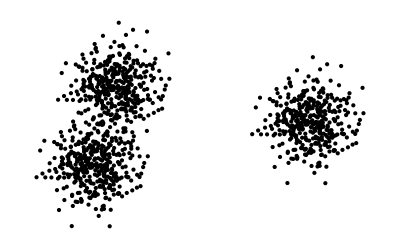

```mathematica
Graphics[Map[Point[#]&,ndOv[2,1]]]
```

```mathematica
(*Export["overlapped2D.tsv",ndOv[2,1]]*)
```

## 2D, unbalanced

```mathematica
ndUb[3]=Join[Map[#+{1,6}&,nd[2][400]],Map[#*0.5&,nd[2][400]],Map[#+{10,2}&,nd[2][400]]];
```

```mathematica
Dimensions[ndUb[3]]
```

{1200,2}

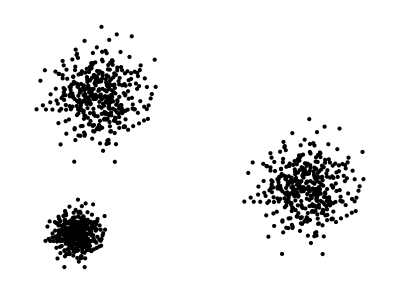

```mathematica
Graphics[Map[Point[#]&,ndUb[3]]]
```

```mathematica
(*Export["unbalanced2D.tsv",ndUb[3]]*)
```

```mathematica
(*Export["unbalanced2D_x10.tsv",ndUb[3]*10]*)
```

```mathematica
(*Export["unbalanced2D_x10E-1.tsv",ndUb[3]/10]*)
```

## 2D, subcluster

```mathematica
ndSubs[5]=Join[Map[#+{0,0}&,nd[2][400]],Map[#*1.1+{0,6}&,nd[2][400]],Map[#*1.2+{18,0}&,nd[2][400]],Map[#+{17,6}&,nd[2][400]],Map[#*1.4+{7,17}&,nd[2][400]]];
```

```mathematica
Dimensions[ndSubs[5]]
```

{2000,2}

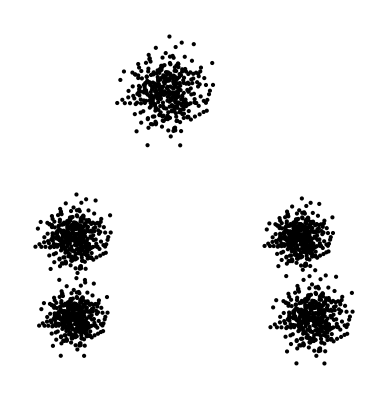

```mathematica
Graphics[Map[Point[#]&,ndSubs[5]]]
```

```mathematica
(*Export["subcluster2D.tsv",ndSubs[5]]*)
```

subcluster2D.tsv

## 2D, noisy

```mathematica
shifts={{6.8,2.5},{4.5,6.1},{4.0,3.2},{2.0,1.7},{8.5,4.8},{2.0,5.4},{5.9,0.3}}
```

{{6.8,2.5},{4.5,6.1},{4.,3.2},{2.,1.7},{8.5,4.8},{2.,5.4},{5.9,0.3}}

```mathematica
scales={0.25,0.3,0.18,0.3,0.28,0.3,0.3}
```

{0.25,0.3,0.18,0.3,0.28,0.3,0.3}

```mathematica
(nd[7,"correct"]=Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}])//Length
```

7

```mathematica
nd[7,"correct","centroids"]=Map[Mean[#]&,nd[7,"correct"]]
```

{{6.79649,2.50192},{4.49579,6.1023},{3.99747,3.20138},{1.99579,1.7023},{8.49607,4.80215},{1.99579,5.4023},{5.89579,0.302305}}

```mathematica
nd[7,"correct","1/10","centroids"]=Map[Mean[#]&,nd[7,"correct"]/10]
```

{{0.679649,0.250192},{0.449579,0.61023},{0.399747,0.320138},{0.199579,0.17023},{0.849607,0.480215},{0.199579,0.54023},{0.589579,0.0302305}}

```mathematica
(nd[7]=Flatten[Table[Map[#*scales[[n]]+shifts[[n]]&,nd[2][200]],{n,Length[shifts]}],1])//Dimensions
```

{1400,2}

```mathematica
(nd[7,"correct","R"]=createClusterdFileR[nd[7,"correct"]])//Length
```

1400

```mathematica
(nd[7,"correct","R","1/10"]=createClusterdFileR[nd[7,"correct"]/10])//Length
```

1400

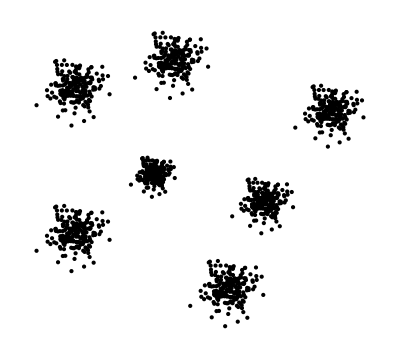

```mathematica
Graphics[Map[Point[#]&,nd[7]],PlotRange->All]
```

```mathematica
(*Export["nd7.tsv",nd[7]]*)
```

```mathematica
(*Export["nd7_x10E-1.tsv",nd[7]/10]*)
```

```mathematica
nd[7,"correct","R"]//Length
```

1400

```mathematica
(*Export["nd7_correct_R.tsv",nd[7,"correct","R"]]*)
```

```mathematica
(*Export["nd7_correct_R.cent.tsv",nd[7,"correct","centroids"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.tsv",nd[7,"correct","R","1/10"]]*)
```

```mathematica
(*Export["nd7_correct_R_x10E-1.cent.tsv",nd[7,"correct","1/10","centroids"]]*)
```

```mathematica
FindClusters[nd[7],Method->"Agglomerate"]//Length
```

1

```mathematica
nois=Map[#+{5,3.2}&,bg[2][400]*5.4];
```

```mathematica
noisy[7]=Join[nd[7],nois];
```

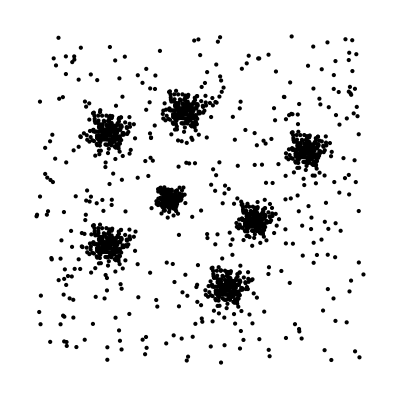

```mathematica
Graphics[Map[Point[#]&,noisy[7]]]
```

```mathematica
(*Export["noisy7.tsv",noisy[7]]*)
```

```mathematica
(*Export["noisy7_x10E-1.tsv",noisy[7]/10]*)
```

```mathematica
FindClusters[noisy[7],7,Method->"Optimize"]//Length
```

7

```mathematica
FindClusters[noisy[7],Method->"Agglomerate"]//Length
```

1

```mathematica
FindClusters[noisy[7],Method->"Optimize"]//Length
```

2

## 2D, 60 samples, 6 clusters, each cluster has 10 samples.

わかりやすいデータ、6クラスタ、60サンプル、各クラスタに10メンバー、2次元

```mathematica
rt6=Map[polarToxy[{1,#}]&,Table[2 Pi n/6,{n,1,6}]]
```

{{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}}

```mathematica
Graphics[Map[Point[#]&,rt6]]
```

-Graphics-

```mathematica
dataCLrt6=Transpose[Table[rt6,{10}]]
```

{{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2}},{{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2}},{{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0}},{{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2}},{{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2}},{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}}

```mathematica
dataFLrt6=Flatten[dataCLrt6,1]
```

{{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1,0},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1/2,-(√3)/2},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
(*Export["dataFLrt6.tsv",dataFLrt6]*)
```

## 2D, 50 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table5=Transpose[Table[rt10,{5}]];
```

```mathematica
rt10table5R=makeRClusterFromMMAClData[rt10table5]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table5R.tsv",rt10table5R]*)
```

```mathematica
Directory[]
```

/Users/amanokou

## 2D, 100 samples, 10 clusters

```mathematica
rt10=Map[polarToxy[{1,#}]&,Table[2 Pi n/10,{n,1,10}]]//N
```

{{0.809017,0.587785},{0.309017,0.951057},{-0.309017,0.951057},{-0.809017,0.587785},{-1.,0.},{-0.809017,-0.587785},{-0.309017,-0.951057},{0.309017,-0.951057},{0.809017,-0.587785},{1.,0.}}

```mathematica
rt10table10=Transpose[Table[rt10,{10}]];
```

```mathematica
rt10table10R=makeRClusterFromMMAClData[rt10table10]
```

{{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.809017,0.587785,1},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{0.309017,0.951057,2},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.309017,0.951057,3},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-0.809017,0.587785,4},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-1.,0.,5},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.809017,-0.587785,6},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{-0.309017,-0.951057,7},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.309017,-0.951057,8},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{0.809017,-0.587785,9},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10},{1.,0.,10}}

```mathematica
(*Export["rt10table10R.tsv",rt10table10R]*)
```

```mathematica
Directory[]
```

/Users/amanokou

## 10D, 100 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table10=Transpose[Table[id10,{10}]];
```

```mathematica
id10Table10R=makeRClusterFromMMAClData[id10Table10]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## 10D, 50 samples, 10 clusters

```mathematica
id10=IdentityMatrix[10];
```

```mathematica
id10Table5=Transpose[Table[id10,{5}]];
```

```mathematica
id10Table5R=makeRClusterFromMMAClData[id10Table5]
```

{{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,1,0,0,0,0,0,0,0,0,2},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,1,0,0,0,0,0,0,0,3},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,1,0,0,0,0,0,0,4},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,1,0,0,0,0,0,5},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,1,0,0,0,0,6},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,1,0,0,0,7},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,1,0,0,8},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,1,0,9},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10},{0,0,0,0,0,0,0,0,0,1,10}}

## TEST